```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
datafull=Import["../data/PLTCM_num.csv",HeaderLines->2];
datafull[[1]]
Dimensions@datafull
```

{3681,8,18000721-03000,327571,4,26,1222.64,4.48514,1.10517,1351.22,19.0359,1802.82,75.8486,120,2.68249,,0,,2,207254,0,678.897,1,1224.67,05.01.18 17:04,1.10509,0,NOOIL,,1,606,421,317,4.48514,1262.69,438.601,1222.64,1772}

{86222,38}

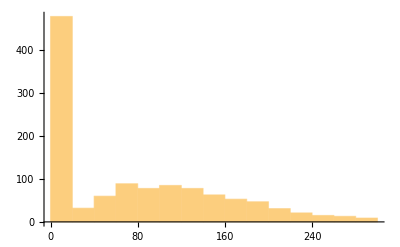

```mathematica
Histogram@Values@Counts@datafull[[All,1]]
```

```mathematica
nullpos=Position[datafull[[All,34]],_?(Head@#==String&)];
datafull=Delete[datafull,nullpos];
```

```mathematica
mostlyzeropos=Position[datafull[[All,11]],_?(#==0&)][[{2,3}]];
datafull=Delete[datafull,mostlyzeropos];
```

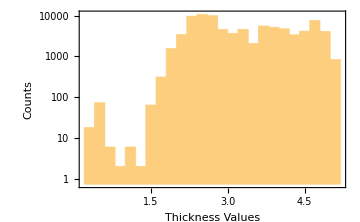
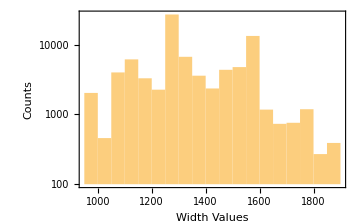

```mathematica
{Histogram[datafull[[All,34]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafull[[All,35]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]}
```

```mathematica
datafull[[Flatten@Position[datafull[[All,11]],_?Negative],11]]*=(-1);
```

```mathematica
density[thick_,width_,length_,weight_]:=N@weight/(thick*width*length);
```

```mathematica
thickvaluesthkpos=datafull[[All,34]];
widthvaluesthkpos=datafull[[All,35]];
lengthvaluesthkpos=datafull[[All,36]];
weightvaluesthkpos=datafull[[All,11]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
KeySort@Counts@densities
```

<|0.→20,9.76762×10^-13→1,1.2917×10^-11→1,1.35301×10^-11→1,1.64027×10^-11→1,2.53845×10^-11→1,2.67805×10^-11→1,4.91618×10^-11→1,1.09961×10^-10→1,1.15293×10^-10→1,1.2598×10^-10→1,1.40149×10^-10→1,84777,8.19799×10^-6→1,8.292×10^-6→1,8.30866×10^-6→1,8.69227×10^-6→1,8.82013×10^-6→1,9.15675×10^-6→1,9.25153×10^-6→1,0.0000111412→1,0.0000112619→1,0.0000145131→2,0.0000352052→1,0.00422551→2|>
 |  |  |  |

```mathematica
(* datafull=datafull[[Flatten@Position[densities,_?(0<#<0.0001&)]]]; *)
```

```mathematica
datafull=datafull[[Flatten@Position[densities,_?(6.5*10^(-6)<#<8.5*10^(-6)&)]]];
```

```mathematica
thickvaluesthkpos=datafull[[All,34]];
widthvaluesthkpos=datafull[[All,35]];
lengthvaluesthkpos=datafull[[All,36]];
weightvaluesthkpos=datafull[[All,11]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
```

```mathematica
Length@densities
Length@Position[densities,_?(#≤6.5*10^(-6)&)]
Length@Position[densities,_?(8.5*10^(-6)≤#<0.0001&)]
Length@Position[densities,_?(6.5*10^(-6)≤#<8.5*10^(-6)&)]
```

65041

0

0

65041

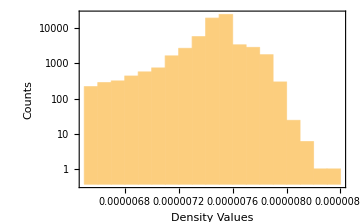

```mathematica
Histogram[densities,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Density Values","Counts"},ImageSize->Medium]
```

```mathematica
datafull=Delete[datafull,Position[datafull[[All,25]],""]];
```

```mathematica
secondscolumn=Table[AbsoluteTime[{datafull[[i,25]],{"Day",".","Month",".","YearShort"," ","Hour",":","Minute"}}],{i,Length@datafull}];
datafull=Join[datafull,Partition[secondscolumn,1],2];
datafullsorted=Sort[datafull,#1[[1]]<#2[[1]]&];
```

Deletion of sequences less than 50

```mathematica
deletepos4=Flatten@Table[Position[datafullsorted[[All,1]],i],{i,Keys@Cases[Normal@Counts@datafullsorted[[All,1]],_?(Values[#]<50&)]}];
datafullsorted=Delete[datafullsorted,Partition[deletepos4,1]];
```

```mathematica
Dimensions@datafullsorted
```

{59604,39}

```mathematica
programids=DeleteDuplicates@datafullsorted[[All,1]];
Length@programids
datafullsortedfinal=Flatten[Table[Sort[Select[datafullsorted,#[[1]]==i&],#1[[39]]<#2[[39]]&],{i,programids}],1];
Dimensions@datafullsortedfinal
```

524

{59604,39}

```mathematica
datafullsortedfinal[[1]]
```

{3609,8,17169021-06000,319652,4,38,1472.14,2.51248,0.468514,689.719,18.2915,3427.1,76.5568,31.2446,2.11253,,0,,2,207148,0,713.984,1,1473.2,29.12.17 18:19,0.468521,0,QUAKEREGL1,,1,610,331,241,2.51248,1535.35,620.727,1472.14,3302,3723560340}

```mathematica
datafullsortedfinal[[All,7]]==datafullsortedfinal[[All,35]]
datafullsortedfinal[[All,7]]==datafullsortedfinal[[All,37]]
```

False

False

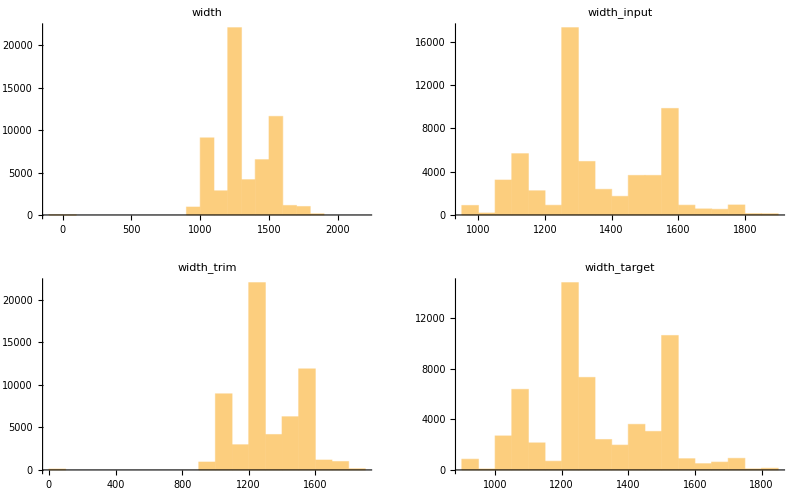

```mathematica
GraphicsGrid[{{Histogram[datafullsortedfinal[[All,7]],PlotLabel->"width"],
Histogram[datafullsortedfinal[[All,35]],PlotLabel->"width_input"]},{Histogram[datafullsortedfinal[[All,24]],PlotLabel->"width_trim"],Histogram[datafullsortedfinal[[All,37]],PlotLabel->"width_target"]}}]
```

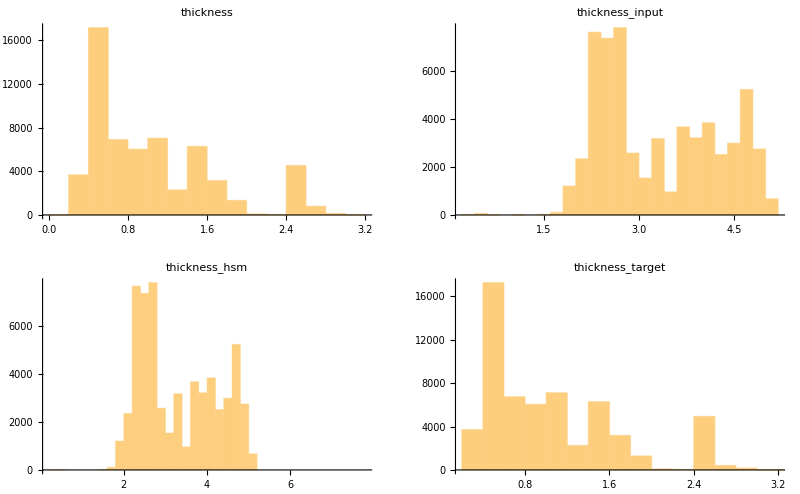

```mathematica
GraphicsGrid[{{Histogram[datafullsortedfinal[[All,9]],PlotLabel->"thickness"],
Histogram[datafullsortedfinal[[All,34]],PlotLabel->"thickness_input"]},{Histogram[datafullsortedfinal[[All,8]],PlotLabel->"thickness_hsm"],Histogram[datafullsortedfinal[[All,26]],PlotLabel->"thickness_target"]}}]
```

```mathematica
data=Join[Partition[Range@Length@datafullsortedfinal,1],datafullsortedfinal[[All,{1}]],ConstantArray[{0,0,0,0,0,0},Length@datafullsortedfinal],datafullsorted[[All,{35,34,25,39}]],ConstantArray[{0},Length@datafullsortedfinal],datafullsorted[[All,{6,26,37,8,9,24,7,4,3,11,12}]],2];
```

```mathematica
data[[1]]
```

{1,3609,0,0,0,0,0,0,1264.04,2.55459,30.12.17 02:14,3723588840,0,26,0.477622,1222.64,2.55459,0.477354,1224.67,1222.64,318580,17167961-03000,13.5754,2998.57}

```mathematica
Dimensions@data
```

{59604,24}

```mathematica
(* Export["pltcm_manipulated_64026.csv",data] *)
```

```mathematica
Export["../data/pltcm_manipulated_59604_rev1.csv",data];
```